```mathematica
ω1=920;ω2=1550;
s1=0.9^2/2;s2=0.556^2/2;
dt = 0.01/ω2;
period =2π/ω1;
tmax=100 period;
nmax = tmax/dt;
ω0=18500;
gamma = 375;
data=Table[{n dt,Exp[-(s1(1-Exp[-I ω1 (n dt)])+s2(1-Exp[-I ω2 (n dt)]))-I ω0 (n dt)-gamma *(n dt)]},{n,0,nmax}];
{time,func}=Transpose[data];
s=Fourier[func,FourierParameters->{-1, 1}];
```

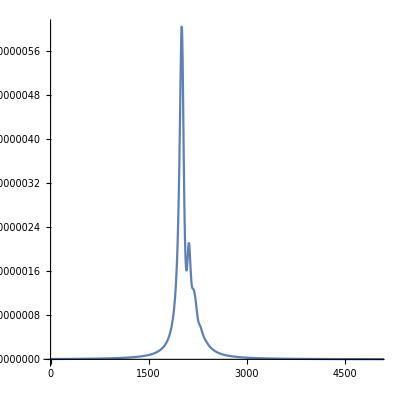

```mathematica
ListLinePlot[{Abs[s]^2},PlotRange->{{0,5000},All},AspectRatio->1]
```

```mathematica
ListLinePlot[{Re[s],Im[s],Abs[s],Abs[s]^2},PlotRange->{{0,5000},All},AspectRatio->1]
```

-Graphics-

```mathematica
Options[fourierData]={FourierParameters->{-1,1}};

fourierData[data_?MatrixQ,OptionsPattern[]]:=Module[{xGrid,pGrid,f,x0,x1,NN,DFT},{xGrid,f}=Transpose[data];
{x0,x1}=MinMax[xGrid];
NN=Length[xGrid]-1;
pGrid=RotateRight[Range[-NN/2,NN/2] 2.0 π/(x1-x0),Quotient[NN,2]];
DFT=Fourier[f,FourierParameters->OptionValue[FourierParameters]] (x1-x0)/Sqrt[2 π (NN)];
Transpose@{pGrid,Abs@DFT}]
```

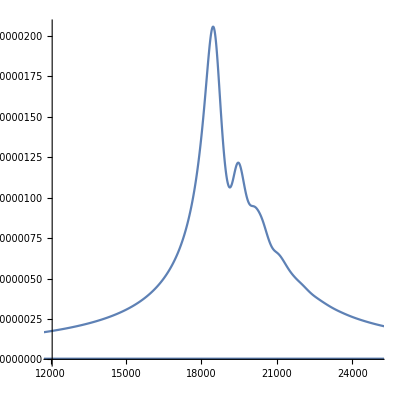

```mathematica
ListLinePlot[fourierData[data],PlotRange->{{12000,25000},All},AspectRatio->1]
```

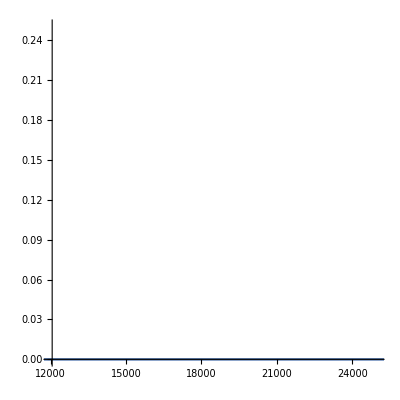

```mathematica
ListLinePlot[fourierData[data],PlotRange->{{12000,25000},{0,0.25}},AspectRatio->1]
```

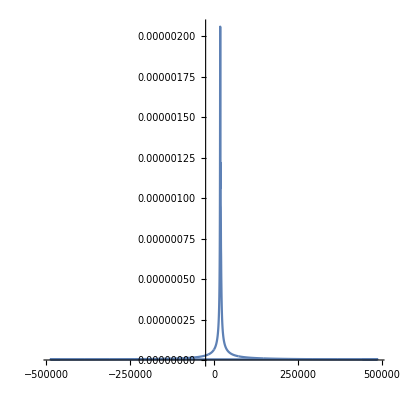

```mathematica
ListLinePlot[fourierData[data],PlotRange->{{-12000,-25000},{0,0.25}},AspectRatio->1]
```

```mathematica
{s1,s2}
```

{0.405,0.154568}

```mathematica
Range[-5,5]
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5}